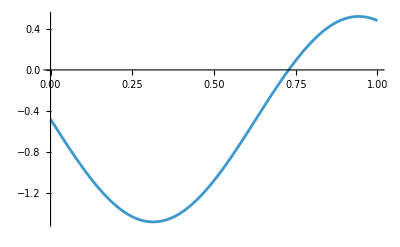

```mathematica
f[s_]:=-Sin[5s]+Sin[5]/2
Plot[f[s],{s,0,1}]
```

```mathematica
sa=FindRoot[f[s]==0,{s,1/2}][[1,2]]
fi0=Integrate[f[s],{s,0,sa}]
fi[ss_]=Integrate[f[s],{s,0,ss}]-fi0
```

0.728327

-0.724718

0.724718+1/10 (-2+2 Cos[5 ss]+5 ss Sin[5])

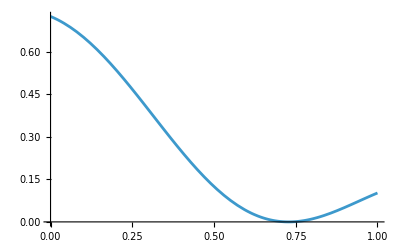

```mathematica
gr1=Plot[fi[s],{s,0,1}]
```

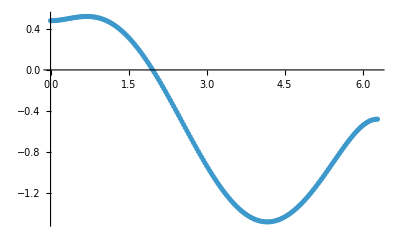

```mathematica
SetDirectory[NotebookDirectory[]];
pair[ls1_,ls2_]:=Transpose[{ls1,ls2}];
xy=ReadList["dat.dat",{Number,Number}];
x=Transpose[xy][[1]];
y=Transpose[xy][[2]];
gr2=ListPlot[pair[x,y]]
```

```mathematica
Plot[f[s],{s,0,1},PlotRange->All]
```

-Graphics-

```mathematica
a=Pi/(fi[1]-fi[0])fi[1]-Pi/2;
b=FindRoot[Cot[b]==a-b,{b,-Pi/4}][[1,2]]
u0=(fi[1]-fi[0])/4/Pi/Sin[b]
c1=fi[1]-2u0 Cos[b]
```

-0.589201

0.0891767

-0.0462924

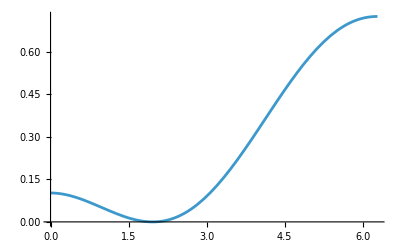

-Graphics-

```mathematica
g[s_]:=2u0 Cos[s-b]-(fi[1]-fi[0])*s/2/Pi+c1
Plot[g[s],{s,0,2Pi}]
Plot[fi[s],{s,0,1}]
```

```mathematica
gama=Pi+2b
zero=Pi+gama/2
FindRoot[g[s]==fi[0],{s,zero}]
```

1.96319

4.12319

{s→6.28319}

```mathematica
err=1;
iter=0;
While[err>10^(-12),
err=Abs[g[zero]-fi[0]];
zero-=(g[zero]-fi[0])/g'[zero];
Print[err," ",iter];
iter++;
If[iter>10,Break[]]
]
```

0.362359 0

0.0607882 1

0.015306 2

0.00391627 3

0.000996603 4

0.00025185 5

0.0000633371 6

0.0000158836 7

3.97724×10^-6 8

9.95112×10^-7 9

2.48879×10^-7 10

```mathematica
zero
```

6.28227

```mathematica
g[zero]+fi[0]
```

1.44944

```mathematica
fi[0]
```

0.724718

```mathematica
u0
b
(fi[1]-fi[0])
c1
```

0.0891767

-0.589201

-0.62273

-0.0462924